## Full phase diagram in three-level system

```mathematica
ham[Δ,Ω,c]//MatrixForm
```

(-ⅈ+Δ | -c | Ω/2
-c | ⅈ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

```mathematica
EP2Surf[Δ_,Ω_,c_]:=Simplify[Discriminant[Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,Ω,c]
```

1/4 (16 c^6-16 Δ^4+72 c^3 Δ Ω^2-8 c^4 (6+4 Δ^2-3 Ω^2)+2 (-2+Ω^2)^3+Δ^2 (-32-40 Ω^2+Ω^4)-2 c Δ Ω^2 (4 Δ^2+9 (4+Ω^2))+c^2 (48+16 Δ^4-48 Ω^2-15 Ω^4+8 Δ^2 (8+5 Ω^2)))

```mathematica
Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,0];
```

e^3-2 e^2 Δ+(c Ω^2)/2+(Δ Ω^2)/2+e (1-c^2+Δ^2-Ω^2/2)

```mathematica
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

4 Δ^3+27 c Ω^2+9 Δ (4-4 c^2+Ω^2)

```mathematica
EP2Surf[x,y,z]
```

1/4 (2 y^6-8 x^3 y^2 z-18 x y^2 z (4+y^2-4 z^2)+16 x^4 (-1+z^2)+24 y^2 (-1+z^2)^2+16 (-1+z^2)^3-3 y^4 (4+5 z^2)+x^2 (y^4+40 y^2 (-1+z^2)-32 (-1+z^2)^2))

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[Δ,Ω,c]]==0,{Δ,-1,0.5},{Ω,0,2.5},{c,0,3},PlotPoints->100,Mesh->None,PlotRange->All,ContourStyle->Directive[Lighter@Blue,Opacity[0.7],Lighting->"Accent"]],
Frame->True,AxesLabel->{"Δ/γ","Ω/γ","c/γ"},Boxed->True,AxesStyle->Directive[Black,18],ImageSize->300]
```

-Graphics3D-

```mathematica
RealSurf=ContourPlot3D[4 Δ^3+27c Ω^2+9 Δ (4-4 c^2+Ω^2)==0,{Δ,-1,0.5},{Ω,0,2.5},{c,0,3},RegionFunction->Function[{x,y,z},Evaluate[EP2Surf[x,y,z]<0]],RegionBoundaryStyle->None,ContourStyle->{Lighter@Green,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
CDeltaSurf=ContourPlot3D[c==-Δ,{Δ,-1,0.5},{Ω,0,2.5},{c,0,3},RegionBoundaryStyle->None,ContourStyle->{Lighter@Red,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
Show[P1,RealSurf,PlotRange->All]
```

-Graphics3D-

```mathematica
EP3EqC=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,c],ReEquSurf,c]]];
EP3ProjLineC=EP3EqG[[2,1]];
EP3G0=FactorList[EP2Surf[Δ,Ω,0]];
ReEquSurf0 = FactorList[4 Δ^3+9 Δ (4+Ω^2)];
EP3ProjLineG=EP3EqG[[2,1]]
EP3G0[[3,1]]
```

512 Δ^6+1728 Δ^4 Ω^2-1458 Ω^4+1944 Δ^2 Ω^4+729 Ω^6

16+32 Δ^2+16 Δ^4-24 Ω^2+40 Δ^2 Ω^2+12 Ω^4-Δ^2 Ω^4-2 Ω^6

```mathematica
P3=Show[ContourPlot[{EP3ProjLineC==0},{Δ,-1,0},{Ω,0,2.5},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]}}],
ContourPlot[{EP3G0[[3,1]]==0},{Δ,-1,0.5},{Ω,0,2.5},PlotPoints->50,ContourStyle->{{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
ContourPlot[{ReEquSurf0[[3,1]]==0},{Δ,-1,0.5},{Ω,0,1.4},PlotPoints->50,ContourStyle->{{RGBColor[0,0.8,0,1],Thickness[0.01]}}],
ContourPlot[{ReEquSurf0[[2,1]]==0},{Δ,-1,0.5},{Ω,0,1.4},PlotPoints->50,ContourStyle->{{RGBColor[0,0.8,0,1],Thickness[0.01]}}]];
```

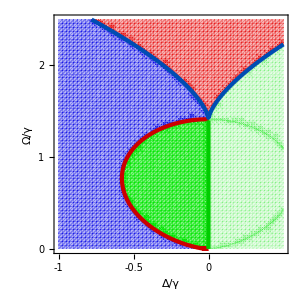

```mathematica
P4=Show[
RegionPlot[EP3ProjLineC<0 && ReEquSurf0[[2,1]]>0,{Δ,-1,0.5},{Ω,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.1]}],
RegionPlot[EP3ProjLineC>0 && ReEquSurf0[[2,1]]>0&&EP3G0[[3,1]]>0,{Δ,-1,0.5},{Ω,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.1]}],
RegionPlot[EP3ProjLineC<0 && ReEquSurf0[[2,1]]<0,{Δ,-1,0.5},{Ω,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.5]}],
RegionPlot[EP3ProjLineC>0 &&EP3G0[[3,1]]<0,{Δ,-1,0.5},{Ω,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0.9,0,0,.3]}],
RegionPlot[EP3ProjLineC>0 &&EP3G0[[3,1]]>0&&ReEquSurf0[[2,1]]<0,{Δ,-1,0.5},{Ω,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,0.9,.3]}],
P3,Frame->True,FrameLabel->{"Δ/γ","Ω/γ"},PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{-1,-0.5,0},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1,0.5},{0,2.5}},ImageSize->300]
```

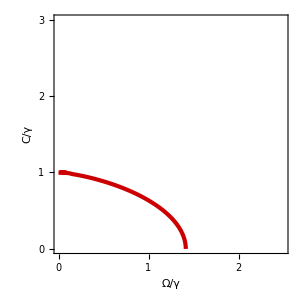

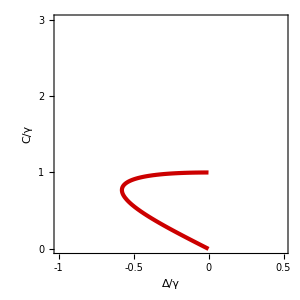

```mathematica
EP3EqDelta=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,c],ReEquSurf,Δ]]];
EP3EqOmega=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,c],ReEquSurf,Ω]]];
P5=Show[ContourPlot[{EP3EqDelta==0},{Ω,0,2.5},{c,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]}}], FrameLabel->{"Ω/γ","C/γ"}, FrameStyle->Directive[Black,18,Thickness[0.0039]], ImageSize->300,FrameTicks->{{{0,1,2,3},None},{{0,1,2},None}}]
P6=Show[ContourPlot[{EP3EqOmega==0},{Δ,-1,0},{c,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]}}],FrameLabel->{"Δ/γ","C/γ"}, FrameStyle->Directive[Black,18,Thickness[0.0039]], PlotRange->{{-1,0.5},{0,3}}, ImageSize->300, FrameTicks->{{{0,1,2,3},None},{{-1,-0.5,0, 0.5},None}}]
```

## 2D Ω slice cut

```mathematica
Ω0=3/5;
Ω1=2+2/5;
```

```mathematica
cs01=Flatten[Δ/.Solve[(512 Δ^6+1728 Δ^4 Ω^2-1458 Ω^4+1944 Δ^2 Ω^4+729 Ω^6/.Ω->Ω0)==0,Δ]][[1]];
cs11=Flatten[Δ/.Solve[(512 Δ^6+1728 Δ^4 Ω^2-1458 Ω^4+1944 Δ^2 Ω^4+729 Ω^6/.Ω->Ω1)==0,Δ]][[1]];
cs12=Flatten[Δ/.Solve[(16+32 Δ^2+16 Δ^4-24 Ω^2+40 Δ^2 Ω^2+12 Ω^4-Δ^2 Ω^4-2 Ω^6/.Ω->Ω1)==0,Δ]][[1]];
```

```mathematica
0.975-0.15
```

0.825

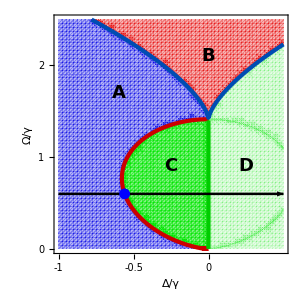

```mathematica
P5=Show[P4,With[{Ω=Ω0},Graphics[{Black,Thickness[0.006],Arrow[{{-1,Ω},{0.5,Ω}}]}]],With[{Δ=cs01},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs01,Ω0},{cs01,Ω0}}]}]],Graphics[{Text[Style["A",FontFamily->"Arial",Bold,18],{-0.6,1.7}]}],
Graphics[{Text[Style["B",FontFamily->"Arial",Bold,18],{0,2.1}]}],
Graphics[{Text[Style["C",FontFamily->"Arial",Bold,18],{-0.25,0.9}]}],
Graphics[{Text[Style["D",FontFamily->"Arial",Bold,18],{0.25,0.9}]}]]
```

```mathematica
Export["/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3b.png",P5]
```

/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3b.png

```mathematica
compcond=Simplify[Discriminant[Det[ham[Δ,Ω0,c]-IdentityMatrix[3]e],e]]
```

-68921/31250+4 c^6+(162 c^3 Δ)/25-(28919 Δ^2)/2500-4 Δ^4+c^4 (-246/25-8 Δ^2)-(9 c Δ (981+100 Δ^2))/1250+c^2 (3597/500+(98 Δ^2)/5+4 Δ^4)

```mathematica
Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,c]-IdentityMatrix[3]e],e],e,0];
realcond0=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]/.{Ω->Ω0}
```

e^3-2 e^2 Δ+(c Ω^2)/2+(Δ Ω^2)/2+e (1-c^2+Δ^2-Ω^2/2)

(243 c)/25+9 (109/25-4 c^2) Δ+4 Δ^3

```mathematica
gs=c/.Solve[((243 c)/25+9 (109/25-4 c^2) Δ+4 Δ^3/.{Δ->cs01})==0,c][[2]]
```

```mathematica
(-243/25+3/25 √(6561+392400 Root"0.312"Root[-2421009+3936600 #1+9720000 #1^2+8000000 #1^3&,1]0.3122945341982625+40000 (Root"0.312"Root[-2421009+3936600 #1+9720000 #1^2+8000000 #1^3&,1]0.3122945341982625)^2))/(72 √(Root"0.312"Root[-2421009+3936600 #1+9720000 #1^2+8000000 #1^3&,1]0.3122945341982625)).5
```

0.423055

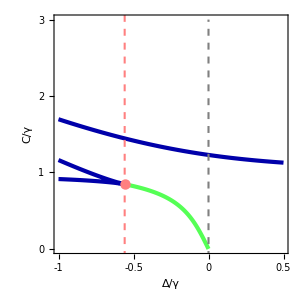

```mathematica
P6=Show[ContourPlot[compcond==0,{Δ,-1,0.5},{c,0,3},PlotPoints->100,ContourStyle->Directive[Darker@Blue,Opacity[1],Thickness[0.01]]],
ContourPlot[realcond0==0,{Δ,cs01,0},{c,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Green,Opacity[1],Thickness[0.01]]],
Graphics[{Dashed,Thickness[0.005],Gray,Line[{{0,-0.3},{0,3}}],Line[{{1,-0.3},{1,3.3}}]}],
With[{Δ=cs01},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs01,N[gs]}}]}]],Graphics[{Pink,Dashed,Thickness[0.005],Line[{{cs01,-0.3},{cs01,3.3}}]}],
Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{-1,-0.5,0, 0.5},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1,0.5},{0,3}},ImageSize->300,FrameLabel->{"Δ/γ","C/γ"}]
```

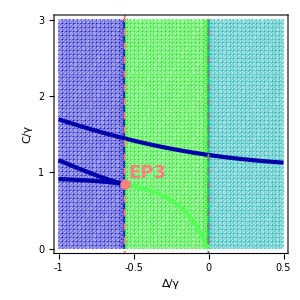

```mathematica
P7=Show[RegionPlot[cs01<Δ<0,{Δ,-1,0.5},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.3]}],
Graphics[{Pink,Text[Style["EP3",FontFamily->"Arial",Bold,18],{cs01+0.15,N[gs]+0.15}]}],
RegionPlot[-1<Δ<cs01,{Δ,-1,0.5},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,0.8,.3]}],RegionPlot[0<Δ<0.5,{Δ,-1,0.5},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.3]}],P6,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,-0.5,-1, 0.5},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1,0.5},{0,3}},ImageSize->300,FrameLabel->{"Δ/γ","C/γ"}]
```